```mathematica
ClearAll["Global`*"];
ClearAll[m];
```

```mathematica
ExtractData[file_]:=Module[{data,shadow,measure,lines,line,xmin,xmax,ymin,ymax,xc,yc,Dc,Dx,Dy,newLine,polarLine,r,rbar,σr,LHratio,area},
data=Import[file];
shadow=EdgeDetect[data,30];(*should test carefully before changing it*)
line=ImageValuePositions[shadow,1]-1024;
{xmin,xmax}=MinMax[line⟦All,1⟧];
{ymin,ymax}=MinMax[line⟦All,2⟧];
{xc,yc}={(xmin+xmax)/2,(ymin+ymax)/2};
Dc=Abs@xc;
{Dx,Dy}={xmax-xmin,ymax-ymin};
LHratio=Dx/Dy;
newLine=Union[line,SameTest->(Norm[#1-#2]<5&)];(*remove very close points*)
polarLine=DeleteDuplicates[{ArcTan[#⟦1⟧-xc,#⟦2⟧],√((#⟦1⟧-xc)^2+(#⟦2⟧)^2)}&/@newLine,#1⟦1⟧==#2⟦1⟧&];
polarLine=Join[Select[SortBy[polarLine,First],#⟦1⟧>0&],{#⟦1⟧+2π,#⟦2⟧}&/@Select[SortBy[polarLine,First],#⟦1⟧<0&]];
r02pi=polarLine[[1,2]];
AppendTo[polarLine,{0,r02pi}];
AppendTo[polarLine,{2π,r02pi}];
r=Interpolation[polarLine,InterpolationOrder->0];
rbar=NIntegrate[r[α]/(2π),{α,0,2π}];
σr=√NIntegrate[(r[α]-rbar)^2/(2π),{α,0,2π}];
area=NIntegrate[1/2 r[α]^2,{α,0,2π}];
{line,xmin,xmax,ymin,ymax,xc,yc,newLine,polarLine,r,Dc,Dx,Dy,LHratio,rbar,σr,area}];
```

```mathematica
FNs=FileNames[FileNameJoin[{NotebookDirectory[],"KerrQED*_bw.png"}]]
```

{D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.00_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.05_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.10_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.15_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.20_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.25_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.30_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.35_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.40_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.45_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.50_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.55_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.60_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.00_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.05_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.10_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.15_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.20_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.25_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.30_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.35_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.40_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.45_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.50_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.55_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.60_bw.png}

```mathematica
FNtab=Table[FNs[[m+13n]],{m,1,13},{n,0,1}]
```

{{D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.00_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.00_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.05_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.05_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.10_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.10_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.15_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.15_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.20_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.20_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.25_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.25_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.30_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.30_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.35_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.35_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.40_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.40_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.45_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.45_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.50_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.50_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.55_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.55_bw.png},{D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQED-0.60_bw.png,D:\常用\广相\课题\新建文件夹 (3)\结果\Qm=0.5\KerrQEDkmax-0.60_bw.png}}

```mathematica
shapedata=Map[ExtractData,FNtab,{2}];
shrink=Table[shapedata[[m,2,-1]]/shapedata[[m,1,-1]],{m,1,13}]
```

{0.605528,0.617176,0.633355,0.651296,0.669529,0.688439,0.707416,0.726456,0.74591,0.765932,0.786404,0.80619,0.826861}

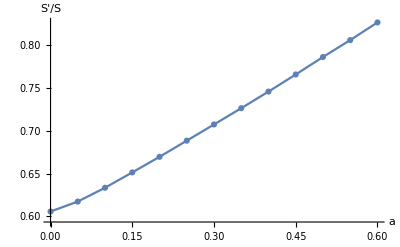

```mathematica
ListLinePlot[Table[{0.05m-0.05,shrink[[m]]},{m,1,13}],AxesLabel->{"a","S'/S"},PlotRange->All,PlotMarkers->Automatic]
```

```mathematica
σk=Table[√(1/(2π)NIntegrate[((shapedata[[m,2,10]][α]-shapedata[[m,1,10]][α])/(shapedata[[m,1,10]][α]))^2,{α,0,2π}]),{m,1,13}]
```

{0.221851,0.215151,0.207022,0.198827,0.191167,0.183565,0.176053,0.168808,0.161309,0.153315,0.144647,0.136124,0.127166}

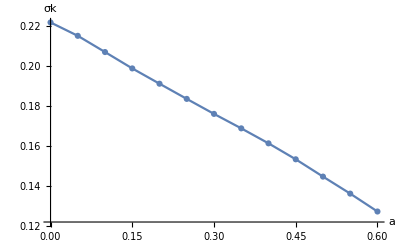

```mathematica
ListLinePlot[Table[{0.05m-0.05,σk[[m]]},{m,1,13}],AxesLabel->{"a","σk"},PlotRange->All,PlotMarkers->Automatic]
```